## 导出数据

```mathematica
SetDirectory[NotebookDirectory[]];
<<extremal.m;
?Extremal`*
```

Loading functions about extremal graphs...

### Data of 1-9

#### test

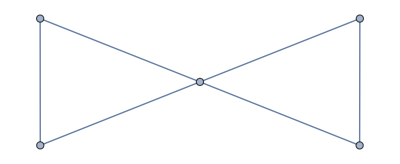

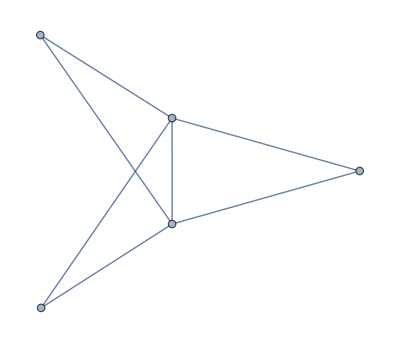
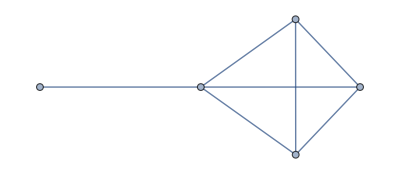
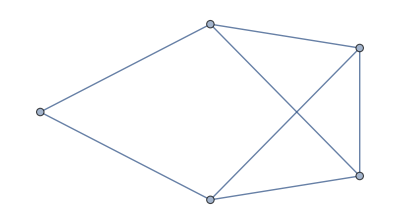
{{-Graphics-,-Graphics-,-Graphics-},7}

```mathematica
graphs=SimpleGraphs[5];
forbidden=GraphF@2
ExtremalGraphs[graphs,forbidden]
```

#### chkQ

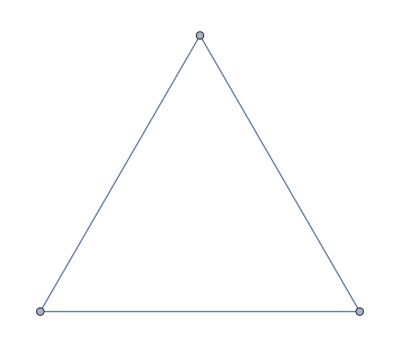
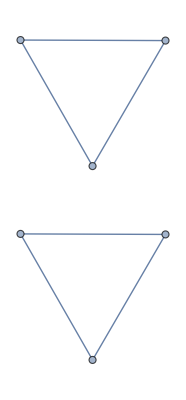
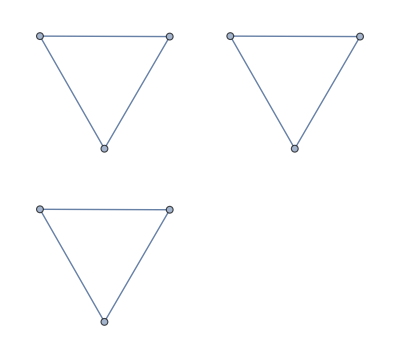

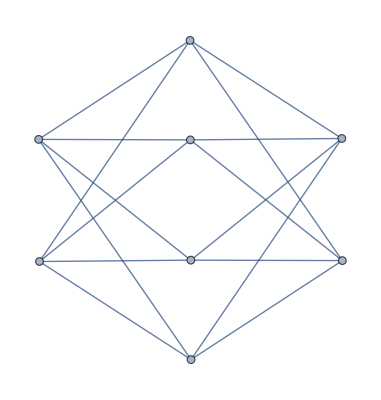
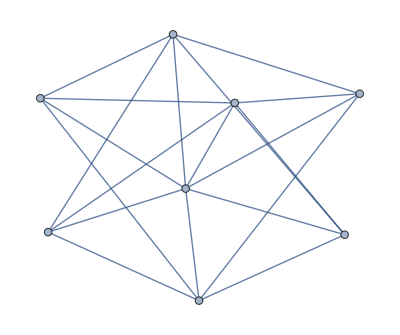
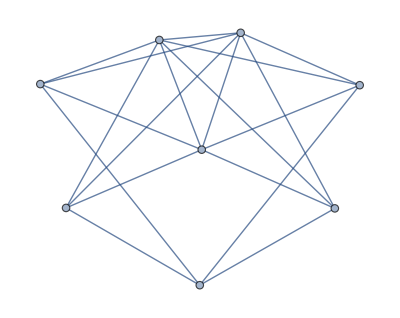
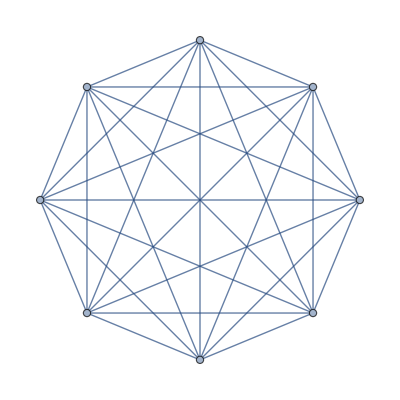
{{{-Graphics-},16},{{-Graphics-,-Graphics-},19},{{-Graphics-},28}}

```mathematica
forbiddens=GraphK3/@Range[3]
graphs=SimpleGraphs@8;
res=ExtremalGraphs[graphs,#]&/@forbiddens
{extremals,edges}={res⟦;;,1⟧,res⟦;;,2⟧};
```